# Seminar 1: Two loads connected with a spring

In this file we compute  motion of two loads connected with a spring in Wolfram Mathematica.
Key moments would be checking conservation of Energy and Momentum. As well checking phasor space and finally making a solid animation of the given task.

## Firstly, we have to define a physical characteristic of the system:

```mathematica
m1=1;m2=1;k=10;l=1;
```

## Secondly, we have to introduce the governing equations:

in the given case - length as instance and motion of equations for both bodies:

```mathematica
le=Sqrt[(x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2];
```

```mathematica
eqs={
m1*x1''[t]-k*(1-l/le)*(x2[t]-x1[t])==0,
m1*y1''[t]-k*(1-l/le)*(y2[t]-y1[t])==0,
m1*z1''[t]-k*(1-l/le)*(z2[t]-z1[t])==0,
m2*x2''[t]+k*(1-l/le)*(x2[t]-x1[t])==0,
m2*y2''[t]+k*(1-l/le)*(y2[t]-y1[t])==0,
m2*z2''[t]+k*(1-l/le)*(z2[t]-z1[t])==0};
```

## If we have differential equations present, one has to provide with initial conditions.

note that in our case we have motion in 3D, therefore we need (2x3) initial condition for each load, or in total 12:

```mathematica
init={
x1[0]==0.6,y1[0]==0,z1[0]==0,
x2[0]==1.5,y2[0]==0,z2[0]==0,
x1'[0]==0,y1'[0]==-0.1,z1'[0]==0,
x2'[0]==0,y2'[0]==+0.1,z2'[0]==0};
```

## Finally we can solve governing equations:

note: DSolve - provides possible analytic solution of the system ;
            NDSolve- provides with numerical solution of the system ;
            Plot[f(x),{x,x_min,x_max}] - graphs the given function in the given range.

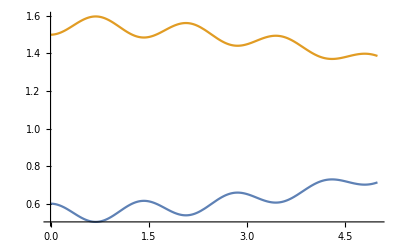

```mathematica
sol=NDSolve[Join[eqs,init],{x1,y1,z1,x2,y2,z2},{t,0,100}];
Plot[{Evaluate[x1[t]]/.sol,Evaluate[x2[t]]/.sol},{t,0,5}]
```

## Now we have to check for the general characteristic of the periodic system

If we have a periodic system its bound to repeat the same motion over and over, therefore we must have same velocity remaining at the same coordinate.
To illustrate that, ParametricPlot[{f(x),f'(x)},{x,x_min,x_max}]  is really handy, since we can directly see what is going on in the phasor space.

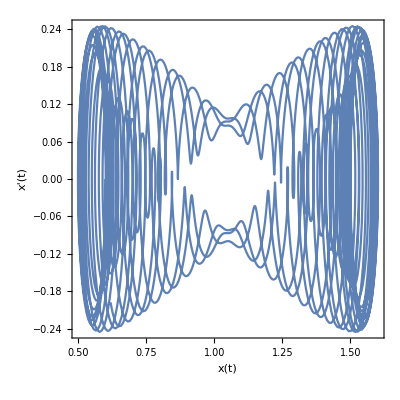

```mathematica
ParametricPlot[{{Evaluate[x1[t]],Evaluate[x1'[t]]}/.sol},{t,0,100},AspectRatio->1,Frame->True,Axes->False,FrameLabel->{"x(t)","x'(t)"}]
```

using ParametricPlot3D we can even see how this coordinates lapse in space as well:

```mathematica
ParametricPlot3D[{{x1[t],y1[t],z1[t]}/.sol,{x2[t],y2[t],z2[t]}/.sol},{t,0,50},PlotStyle->{{Blue},{Red}},BoxRatios->{1,1,1},ViewPoint->Above]
```

-Graphics3D-

## Finally we will attempt to make an animation of the given system:

We consider the loads to be spherical objects, which are connected by a line  and for the extra spice let’s try to add trail which, will follow right after them.

### step 1: we have to create a set of frames, where we can simulate each position configuration of the system. in the similar manner let’s keep track of the trail as well

```mathematica
frames={};
```

```mathematica
trailLength=10;(*Number of trail points to keep*)
trailData1={};
trailData2={};
```

```mathematica
step 2: Now, we can actually simulate each frame and append it to the frame set created above.
```

step 2: Now, we can actually simulate each frame and append it to the frame set created above.

```mathematica
frames=Table[
Module[
{pos1,pos2},
pos1={x1[t],y1[t],z1[t]}/. sol;
pos2={x2[t],y2[t],z2[t]}/. sol;
(*Update the trail data*)
AppendTo[trailData1,pos1];
AppendTo[trailData2,pos2];
If[Length[trailData1]>trailLength,trailData1=Rest[trailData1];];
If[Length[trailData2]>trailLength,trailData2=Rest[trailData2];];
];
Graphics3D[{
{(*Draw the fading trail for Ball 1*)
Table[{Red,Opacity[1-i/trailLength],Sphere[trailData1[[i]],0.025]},{i,1,Length[trailData1]}],
(*Draw the fading trail for Ball 2*)
Table[{Blue,Opacity[1-i/trailLength],Sphere[trailData2[[i]],0.025]},{i,1,Length[trailData2]}]},
{
{Red,Ball[{x1[t],y1[t],z1[t]},0.1]},{Blue,Ball[{x2[t],y2[t],z2[t]},0.1]},Line[{{x1[t],y1[t],z1[t]},{x2[t],y2[t],z2[t]}}]}/. sol,
{Red,Line[Map[Function[Evaluate[{x2[#],y2[#],z2[#]}/. sol]],Range[0,t,0.025]]]}},PlotRange->{{0,2},{-1,1},{-2,2}},ImageSize->Large,Axes->True,Ticks->{True,True,None},TicksStyle->Directive[ Thin,Tiny, Italic],AxesOrigin->{0,0,0},Boxed->False,ViewPoint->Above],{t,0,30}];
```

```mathematica
step 3: Finally, we can play the extracted frames:
```

step 3: Finally, we can play the extracted frames:

```mathematica
ListAnimate[frames]
```

### step 4: Feel free to export files in a preferable format:

```mathematica
Export["simulationextra.gif",frames]
```

simulationextra.gif